```mathematica
dataraw=Import["https://en.wikipedia.org/wiki/List_of_countries_by_GDP_(nominal)","Data"];
```

```mathematica
Position[dataraw,"113,795,678"]
```

{{2,1,2,4,2,2,2}}

```mathematica
datacleaner=dataraw[[2,1,2,4,2]][[3;;,{1,3}]];
```

```mathematica
money=ToExpression[((StringDelete[#,","]&/@ ToString/@datacleaner[[All,2]])/. "—"->0)]/. 0->Missing[]
```

{29184890,18743803,4659929,3912686,4026211,3643834,3162079,2372775,2241253,2179412,2173836,1722746,1712793,1752193,1852723,1323255,1396300,1227544,1237530,914696,936564,Missing[],664564,633267,610118,577389,540380,547387,537079,526411,521642,483727,461618,476388,450119,429457,421972,418542,407107,400261,382768,373072,345037,389050,330267,436906,308683,299836,289222,288406,263620,257145,279641,260236,222905,217983,190741,Missing[],187760,154431,160227,141776,114965,124499,124282,124676,125842,113200,163698,112212,80397,Missing[],106943,95350,98963,92526,93197,86538,89084,86260,84869,64240,82825,78780,80962,70749,74316,72485,75962,74080,53652,49668,53410,53352,51327,50183,46353,47737,46636,42914,43521,44458,42765,36333,44188,37094,35365,33776,33463,32267,25224,32538,49910,25334,26326,28343,27178,23250,26429,25787,24836,23586,24322,22417,26588,21483,19538,19930,19694,20867,20079,19993,17478,18200,19401,20626,17421,16685,Missing[],17152,Missing[],16503,15463,14953,15720,15833,14205,14252,13372,11009,13711,12109,12766,12508,10767,11149,9623,9926,9995,8980,8070,7548,8288,7165,6975,7431,7139,6910,2162,6402,5841,4892,4750,4672,4086,4714,3649,4040,Missing[],3907,3516,3019,3327,3281,2752,2768,2508,2549,Missing[],2272,2225,Missing[],2120,2167,1881,1832,1761,1745,1735,1546,Missing[],1391,1161,1157,1096,1068,1067,871,764,689,649,509,471,Missing[],Missing[],282,308,280,160,Missing[],62}

```mathematica
(StringSplit[#,"["]&/@datacleaner[[All,1]])[[All,1]]
```

{United States,China ,Germany,India,Japan,United Kingdom,France,Italy,Canada,Brazil,Russia,Spain,South Korea,Australia,Mexico,Turkey,Indonesia,Netherlands,Saudi Arabia,Poland,Switzerland,Taiwan ,Belgium,Argentina,Sweden,Ireland,Israel,Singapore,United Arab Emirates,Thailand,Austria,Norway,Philippines,Vietnam,Bangladesh,Denmark,Malaysia,Colombia,Hong Kong ,South Africa,Romania,Pakistan,Czech Republic,Egypt,Chile,Iran,Portugal,Finland,Peru,Kazakhstan,Algeria,Greece,Iraq,New Zealand,Hungary,Qatar,Ukraine ,Cuba,Nigeria,Morocco,Kuwait,Slovakia,Uzbekistan,Kenya,Dominican Republic,Ecuador,Puerto Rico,Guatemala,Ethiopia,Bulgaria,Angola,Venezuela,Oman,Costa Rica,Sri Lanka,Croatia,Luxembourg,Ivory Coast,Serbia,Panama,Lithuania,Turkmenistan,Ghana,Tanzania ,Uruguay,DR Congo,Azerbaijan,Slovenia,Belarus,Myanmar,Uganda,Bolivia,Tunisia,Jordan,Cameroon,Macau ,Cambodia,Bahrain,Libya,Nepal,Latvia,Paraguay,Estonia,Cyprus ,Zimbabwe,Honduras,El Salvador,Georgia ,Iceland,Senegal,Haiti,Papua New Guinea,Sudan,Guinea,Zambia,Bosnia and Herzegovina,Albania,Burkina Faso,Trinidad and Tobago,Armenia,Guyana,Mongolia,Malta,Mozambique,Mali,Benin,Niger,Jamaica,Nicaragua,Gabon,Lebanon,Syria,Kyrgyzstan,Moldova ,Botswana,Chad,Madagascar,North Macedonia,Yemen,Afghanistan,North Korea,Laos,Brunei,Mauritius,Congo,Bahamas,Tajikistan,Rwanda,Namibia,Malawi,Palestine ,Somalia,Equatorial Guinea,Channel Islands,Mauritania,Kosovo,New Caledonia,Togo,Monaco,Bermuda,Montenegro,Sierra Leone,Liechtenstein,Barbados,Maldives,Isle of Man,Cayman Islands,Guam,Burundi,French Polynesia,Fiji,Eswatini,Liberia,U.S. Virgin Islands,Djibouti,Suriname,Aruba,Andorra,South Sudan,Faroe Islands,Belize,Bhutan,Greenland,Curaçao,Central African Republic,Cape Verde,Gambia,Saint Lucia,Zanzibar,Lesotho,Antigua and Barbuda,Eritrea,Guinea-Bissau,Seychelles,Timor-Leste,San Marino,Solomon Islands,Turks and Caicos Islands,Sint Maarten,Comoros,British Virgin Islands,Grenada,Vanuatu,Saint Vincent and the Grenadines,Northern Mariana Islands,Samoa,Saint Kitts and Nevis,American Samoa,São Tomé and Príncipe,Dominica,Saint Martin,Tonga,Micronesia,Anguilla,Cook Islands,Palau,Kiribati,Marshall Islands,Nauru,Montserrat,Tuvalu}

```mathematica
Interpreter["Country"][#]&/@{"United States","China ","Germany","India","Japan"}
```

{United States,China,Germany,India,Japan}

```mathematica
{{county1,country2, country3},{1,2,3}}//Transpose//TableForm
```

county1 | 1
country2 | 2
country3 | 3

```mathematica
countries=Interpreter["Country"][#]&/@((StringSplit[#,"["]&/@datacleaner[[All,1]])[[All,1]]);
```

```mathematica
countries
```

{United States,China,Germany,India,Japan,United Kingdom,France,Italy,Canada,Brazil,Russia,Spain,South Korea,Australia,Mexico,Turkey,Indonesia,Netherlands,Saudi Arabia,Poland,Switzerland,Taiwan,Belgium,Argentina,Sweden,Ireland,Israel,Singapore,United Arab Emirates,Thailand,Austria,Norway,Philippines,Vietnam,Bangladesh,Denmark,Malaysia,Colombia,Hong Kong,South Africa,Romania,Pakistan,Czech Republic,Egypt,Chile,Iran,Portugal,Finland,Peru,Kazakhstan,Algeria,Greece,Iraq,New Zealand,Hungary,Qatar,Ukraine,Cuba,Nigeria,Morocco,Kuwait,Slovakia,Uzbekistan,Kenya,Dominican Republic,Ecuador,Puerto Rico,Guatemala,Ethiopia,Bulgaria,Angola,Venezuela,Oman,Costa Rica,Sri Lanka,Croatia,Luxembourg,Ivory Coast,Serbia,Panama,Lithuania,Turkmenistan,Ghana,Tanzania,Uruguay,Failure[…],Azerbaijan,Slovenia,Belarus,Myanmar,Uganda,Bolivia,Tunisia,Jordan,Cameroon,Macau,Cambodia,Bahrain,Libya,Nepal,Latvia,Paraguay,Estonia,Cyprus,Zimbabwe,Honduras,El Salvador,Georgia,Iceland,Senegal,Haiti,Papua New Guinea,Sudan,Guinea,Zambia,Bosnia and Herzegovina,Albania,Burkina Faso,Trinidad and Tobago,Armenia,Guyana,Mongolia,Malta,Mozambique,Mali,Benin,Niger,Jamaica,Nicaragua,Gabon,Lebanon,Syria,Kyrgyzstan,Moldova,Botswana,Chad,Madagascar,North Macedonia,Yemen,Afghanistan,North Korea,Laos,Brunei,Mauritius,Democratic Republic of the Congo,Bahamas,Tajikistan,Rwanda,Namibia,Malawi,Palestine,Somalia,Equatorial Guinea,Failure[…],Mauritania,Kosovo,New Caledonia,Togo,Monaco,Bermuda,Montenegro,Sierra Leone,Liechtenstein,Barbados,Maldives,Isle of Man,Cayman Islands,Guam,Burundi,French Polynesia,Fiji,Eswatini,Liberia,United States Virgin Islands,Djibouti,Suriname,Aruba,Andorra,South Sudan,Faroe Islands,Belize,Bhutan,Greenland,Curacao,Central African Republic,Cape Verde,Gambia,Saint Lucia,Failure[…],Lesotho,Antigua and Barbuda,Eritrea,Guinea-Bissau,Seychelles,East Timor,San Marino,Solomon Islands,Turks and Caicos Islands,Sint Maarten,Comoros,British Virgin Islands,Grenada,Vanuatu,Saint Vincent and the Grenadines,Northern Mariana Islands,Samoa,Saint Kitts and Nevis,American Samoa,São Tomé and Príncipe,Dominica,Sint Maarten,Tonga,Micronesia,Anguilla,Cook Islands,Palau,Kiribati,Marshall Islands,Nauru,Montserrat,Tuvalu}

```mathematica
Entity["Country","Germany"]//Head
```

Entity

```mathematica
supercleanData=Select[Transpose[{countries,money}],Head[#[[1]]]===Entity&]
```

{{United States,29184890},{China,18743803},{Germany,4659929},{India,3912686},{Japan,4026211},{United Kingdom,3643834},{France,3162079},{Italy,2372775},{Canada,2241253},{Brazil,2179412},{Russia,2173836},{Spain,1722746},{South Korea,1712793},{Australia,1752193},{Mexico,1852723},{Turkey,1323255},{Indonesia,1396300},{Netherlands,1227544},{Saudi Arabia,1237530},{Poland,914696},{Switzerland,936564},{Taiwan,Missing[]},{Belgium,664564},{Argentina,633267},{Sweden,610118},{Ireland,577389},{Israel,540380},{Singapore,547387},{United Arab Emirates,537079},{Thailand,526411},{Austria,521642},{Norway,483727},{Philippines,461618},{Vietnam,476388},{Bangladesh,450119},{Denmark,429457},{Malaysia,421972},{Colombia,418542},{Hong Kong,407107},{South Africa,400261},{Romania,382768},{Pakistan,373072},{Czech Republic,345037},{Egypt,389050},{Chile,330267},{Iran,436906},{Portugal,308683},{Finland,299836},{Peru,289222},{Kazakhstan,288406},{Algeria,263620},{Greece,257145},{Iraq,279641},{New Zealand,260236},{Hungary,222905},{Qatar,217983},{Ukraine,190741},{Cuba,Missing[]},{Nigeria,187760},{Morocco,154431},{Kuwait,160227},{Slovakia,141776},{Uzbekistan,114965},{Kenya,124499},{Dominican Republic,124282},{Ecuador,124676},{Puerto Rico,125842},{Guatemala,113200},{Ethiopia,163698},{Bulgaria,112212},{Angola,80397},{Venezuela,Missing[]},{Oman,106943},{Costa Rica,95350},{Sri Lanka,98963},{Croatia,92526},{Luxembourg,93197},{Ivory Coast,86538},{Serbia,89084},{Panama,86260},{Lithuania,84869},{Turkmenistan,64240},{Ghana,82825},{Tanzania,78780},{Uruguay,80962},{Azerbaijan,74316},{Slovenia,72485},{Belarus,75962},{Myanmar,74080},{Uganda,53652},{Bolivia,49668},{Tunisia,53410},{Jordan,53352},{Cameroon,51327},{Macau,50183},{Cambodia,46353},{Bahrain,47737},{Libya,46636},{Nepal,42914},{Latvia,43521},{Paraguay,44458},{Estonia,42765},{Cyprus,36333},{Zimbabwe,44188},{Honduras,37094},{El Salvador,35365},{Georgia,33776},{Iceland,33463},{Senegal,32267},{Haiti,25224},{Papua New Guinea,32538},{Sudan,49910},{Guinea,25334},{Zambia,26326},{Bosnia and Herzegovina,28343},{Albania,27178},{Burkina Faso,23250},{Trinidad and Tobago,26429},{Armenia,25787},{Guyana,24836},{Mongolia,23586},{Malta,24322},{Mozambique,22417},{Mali,26588},{Benin,21483},{Niger,19538},{Jamaica,19930},{Nicaragua,19694},{Gabon,20867},{Lebanon,20079},{Syria,19993},{Kyrgyzstan,17478},{Moldova,18200},{Botswana,19401},{Chad,20626},{Madagascar,17421},{North Macedonia,16685},{Yemen,Missing[]},{Afghanistan,17152},{North Korea,Missing[]},{Laos,16503},{Brunei,15463},{Mauritius,14953},{Democratic Republic of the Congo,15720},{Bahamas,15833},{Tajikistan,14205},{Rwanda,14252},{Namibia,13372},{Malawi,11009},{Palestine,13711},{Somalia,12109},{Equatorial Guinea,12766},{Mauritania,10767},{Kosovo,11149},{New Caledonia,9623},{Togo,9926},{Monaco,9995},{Bermuda,8980},{Montenegro,8070},{Sierra Leone,7548},{Liechtenstein,8288},{Barbados,7165},{Maldives,6975},{Isle of Man,7431},{Cayman Islands,7139},{Guam,6910},{Burundi,2162},{French Polynesia,6402},{Fiji,5841},{Eswatini,4892},{Liberia,4750},{United States Virgin Islands,4672},{Djibouti,4086},{Suriname,4714},{Aruba,3649},{Andorra,4040},{South Sudan,Missing[]},{Faroe Islands,3907},{Belize,3516},{Bhutan,3019},{Greenland,3327},{Curacao,3281},{Central African Republic,2752},{Cape Verde,2768},{Gambia,2508},{Saint Lucia,2549},{Lesotho,2272},{Antigua and Barbuda,2225},{Eritrea,Missing[]},{Guinea-Bissau,2120},{Seychelles,2167},{East Timor,1881},{San Marino,1832},{Solomon Islands,1761},{Turks and Caicos Islands,1745},{Sint Maarten,1735},{Comoros,1546},{British Virgin Islands,Missing[]},{Grenada,1391},{Vanuatu,1161},{Saint Vincent and the Grenadines,1157},{Northern Mariana Islands,1096},{Samoa,1068},{Saint Kitts and Nevis,1067},{American Samoa,871},{São Tomé and Príncipe,764},{Dominica,689},{Sint Maarten,649},{Tonga,509},{Micronesia,471},{Anguilla,Missing[]},{Cook Islands,Missing[]},{Palau,282},{Kiribati,308},{Marshall Islands,280},{Nauru,160},{Montserrat,Missing[]},{Tuvalu,62}}

```mathematica
plottableData=Rule@@@supercleanData;
```

```mathematica
GeoRegionValuePlot[plottableData]
```

-Graphics-

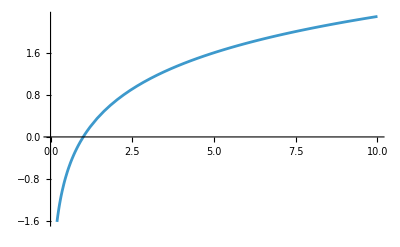

```mathematica
Plot[Log[x],{x,0,10}]
```

```mathematica
#[[1]]->N[Log[#[[2]]]]&/@plottableData
```

{United States→17.1892,China→16.7464,Germany→15.3545}

```mathematica
GeoRegionValuePlot[plottableData]
```

```mathematica
GeoRegionValuePlot[#[[1]]->N[Log[10,#[[2]]]]&/@plottableData,ColorFunction->"TemperatureMap"]
```

-Graphics-